# Name - Vinay Kishor Roll no. - 20201459 Course - B.Sc (H) computer science Regula Falsi

Method of false position : Taking parameters as inputs

x0 = 0

Nmax = 10

epsilon = 0.0001

f[x] := Cos[x]

1th iteration value is :1.412282927437392

Estimated error is :2.

2th iteration value is :1.57390632372288

Estimated error is :0.587717072562608

3th iteration value is :1.5707835219439

Estimated error is :0.16162339628549

4th iteration value is :1.5707963268155

Estimated error is :0.00312280177898

1.5707963267949

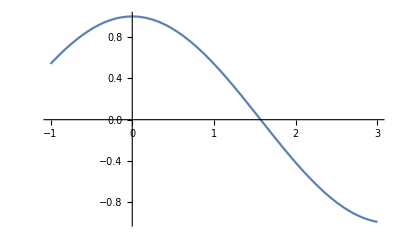

```mathematica
x0 = Input["Enter first guess :"];
x1 = Input["Enter second guess :"];
Nmax =Input["Enter maximum number of iterations :"];
eps = Input["Enter a value of convergence parameter :"];
Print["x0 = ",x0];
Print["Nmax = ",Nmax];
Print["epsilon = ",eps];
f[x_] := Cos[x];
Print["f[x] := ",f[x]];
If[N[f[x0]*f[x1]]>0,
Print["These values do not satisfy the IVP so change the values."],
For[i = 1,i≤Nmax,i++,a = N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0]),16];
If[Abs[(x1-x0)/2]<eps,Return[N[a,16]],
Print[i,"th iteration value is :",N[a,16]];
Print["Estimated error is :",N[x1-x0,16]];
If[f[a]*f[x1]>0,x1 = a, x0 = a]]];
Print["Root is:",N[a,16]];
Print["Estimated error is : ",N[x1-x0,16]]];
Plot[f[x],{x,-1,3}]
```

Method of false position : Constructing a function

```mathematica
falseposition[f_,x0_,x1_,Nmax_,eps_]:= 
If[N[f[x0]*f[x1]]>0,
Print["These values do not satisfy the IVP so change the values."],
y0 = x0;
y1 = x1;
a = y1;
If[Abs[y1-y0]<eps,
Return[N[a,8]],
For[i = 1,i≤ Nmax, i++, a = N[y1-f[y1]*(y1-y0)/(f[y1]-f[y0])];
If[f[a]*f[y1]>0, y1 =a,y0 = a];
If[Abs[y1-y0]<eps,Return[N[a,8]]];
Print[i "th iteration value is : ",N[a,8]];
Print["Estimated error is : ",N[y1-y0,8]]];
Print["Root is : ",N[a,8]];
Print["Estimated error is : ",N[y1-y0,8]]];
Plot[f[x],{x,-1,3}]]




f[x] := Cos[x];
falseposition[f,0,2,5,0.00000001]
```

th iteration value is : 1.41228

Estimated error is : 0.587717

2 th iteration value is : 1.57391

Estimated error is : 0.161623

3 th iteration value is : 1.57078

Estimated error is : 0.0031228

4 th iteration value is : 1.5708

Estimated error is : 0.0000128049

1.5708

Method of false position : Constructing a function

1th iteration value is :1.41228

Estimated error is :0.587717

2th iteration value is :1.57391

Estimated error is :0.161623

3th iteration value is :1.57078

Estimated error is :0.0031228

4th iteration value is :1.5708

Estimated error is :0.0000128049

5th iteration value is :1.5708

Estimated error is :2.05567×10^-11

6th iteration value is :1.5708

Estimated error is :2.05567×10^-11

7th iteration value is :1.5708

Estimated error is :2.05567×10^-11

8th iteration value is :1.5708

Estimated error is :2.05567×10^-11

9th iteration value is :1.5708

Estimated error is :2.05567×10^-11

10th iteration value is :1.5708

Estimated error is :2.05567×10^-11

Root is:1.5708

Estimated error is : 2.05567×10^-11

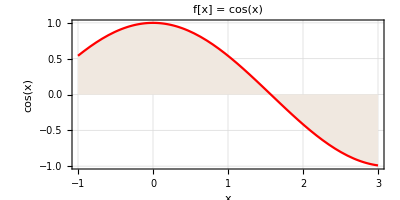

```mathematica
x0 =0;
x1 =2.0;
Nmax =10;
eps =0.000000000001;
f[x_] := Cos[x];
If[N[f[x0]*f[x1]]>0,
Print["These values do not satisfy the IVP so change the values."],
If[Abs[(x1-x0)/2]<eps,Return[N[x1,8]],
For[i = 1,i≤Nmax,i++,a = N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0]),8];
If[f[a]*f[x1]>0,x1 = a, x0 = a];
If[Abs[x1-x0]<eps,Return[N[a,8]]];
Print[i,"th iteration value is :",N[a,8]];
Print["Estimated error is :",N[x1-x0,8]]]];
Print["Root is:",N[a,8]];
Print["Estimated error is : ",N[x1-x0,8]]];
Plot[f[x],{x,-1,3},PlotRange->{-1,1},PlotStyle->Red,PlotLabel->"f[x] =" f[x],
AxesLabel->{x,f[x]},AspectRatio->Automatic,Frame->True,GridLines->Automatic,
ClippingStyle->Automatic, Filling->Axis,FillingStyle->LightBrown]
```